```mathematica
√Sin[x]
```

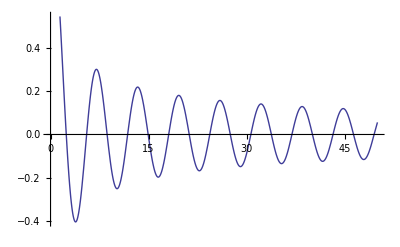

```mathematica
Plot[BesselJ[0,x],{x,0,50}]
```

```mathematica
N[BesselJZero[0,1]]
```

Syntax::bktmop: Expression "TraditionalForm`" has no opening "TraditionalForm`"["".TraditionalForm`""

Syntax::sntxi: Incomplete expression; more input is needed.TraditionalForm`""

```mathematica
N[BesselJZero[0,1000],15]
```

3140.8072952251

```mathematica
zer =BesselJZero[0,Range[1000]]//N
```

{2.40483,5.52008,8.65373,11.7915,14.9309,18.0711,21.2116,24.3525,27.4935,30.6346,33.7758,36.9171,40.0584,43.1998,46.3412,49.4826,52.6241,55.7655,58.907,62.0485,65.19,68.3315,71.473,74.6145,77.756,80.8976,84.0391,87.1806,90.3222,93.4637,96.6053,99.7468,102.888,106.03,109.171,112.313,115.455,118.596,121.738,124.879,128.021,131.162,134.304,137.446,140.587,143.729,146.87,150.012,153.153,156.295,159.437,162.578,165.72,168.861,172.003,175.145,178.286,181.428,184.569,187.711,190.852,193.994,197.136,200.277,203.419,206.56,209.702,212.843,215.985,219.127,222.268,225.41,228.551,231.693,234.835,237.976,241.118,244.259,247.401,250.543,253.684,256.826,259.967,263.109,266.25,269.392,272.534,275.675,278.817,281.958,285.1,288.242,291.383,294.525,297.666,300.808,303.95,307.091,310.233,313.374,316.516,319.657,322.799,325.941,329.082,332.224,335.365,338.507,341.649,344.79,347.932,351.073,354.215,357.357,360.498,363.64,366.781,369.923,373.064,376.206,379.348,382.489,385.631,388.772,391.914,395.056,398.197,401.339,404.48,407.622,410.764,413.905,417.047,420.188,423.33,426.471,429.613,432.755,435.896,439.038,442.179,445.321,448.463,451.604,454.746,457.887,461.029,464.171,467.312,470.454,473.595,476.737,479.879,483.02,486.162,489.303,492.445,495.586,498.728,501.87,505.011,508.153,511.294,514.436,517.578,520.719,523.861,527.002,530.144,533.286,536.427,539.569,542.71,545.852,548.994,552.135,555.277,558.418,561.56,564.702,567.843,570.985,574.126,577.268,580.409,583.551,586.693,589.834,592.976,596.117,599.259,602.401,605.542,608.684,611.825,614.967,618.109,621.25,624.392,627.533,630.675,633.817,636.958,640.1,643.241,646.383,649.524,652.666,655.808,658.949,662.091,665.232,668.374,671.516,674.657,677.799,680.94,684.082,687.224,690.365,693.507,696.648,699.79,702.932,706.073,709.215,712.356,715.498,718.639,721.781,724.923,728.064,731.206,734.347,737.489,740.631,743.772,746.914,750.055,753.197,756.339,759.48,762.622,765.763,768.905,772.047,775.188,778.33,781.471,784.613,787.755,790.896,794.038,797.179,800.321,803.462,806.604,809.746,812.887,816.029,819.17,822.312,825.454,828.595,831.737,834.878,838.02,841.162,844.303,847.445,850.586,853.728,856.87,860.011,863.153,866.294,869.436,872.578,875.719,878.861,882.002,885.144,888.285,891.427,894.569,897.71,900.852,903.993,907.135,910.277,913.418,916.56,919.701,922.843,925.985,929.126,932.268,935.409,938.551,941.693,944.834,947.976,951.117,954.259,957.4,960.542,963.684,966.825,969.967,973.108,976.25,979.392,982.533,985.675,988.816,991.958,995.1,998.241,1001.38,1004.52,1007.67,1010.81,1013.95,1017.09,1020.23,1023.37,1026.52,1029.66,1032.8,1035.94,1039.08,1042.22,1045.37,1048.51,1051.65,1054.79,1057.93,1061.07,1064.21,1067.36,1070.5,1073.64,1076.78,1079.92,1083.06,1086.21,1089.35,1092.49,1095.63,1098.77,1101.91,1105.06,1108.2,1111.34,1114.48,1117.62,1120.76,1123.9,1127.05,1130.19,1133.33,1136.47,1139.61,1142.75,1145.9,1149.04,1152.18,1155.32,1158.46,1161.6,1164.75,1167.89,1171.03,1174.17,1177.31,1180.45,1183.6,1186.74,1189.88,1193.02,1196.16,1199.3,1202.44,1205.59,1208.73,1211.87,1215.01,1218.15,1221.29,1224.44,1227.58,1230.72,1233.86,1237.,1240.14,1243.29,1246.43,1249.57,1252.71,1255.85,1258.99,1262.13,1265.28,1268.42,1271.56,1274.7,1277.84,1280.98,1284.13,1287.27,1290.41,1293.55,1296.69,1299.83,1302.98,1306.12,1309.26,1312.4,1315.54,1318.68,1321.83,1324.97,1328.11,1331.25,1334.39,1337.53,1340.67,1343.82,1346.96,1350.1,1353.24,1356.38,1359.52,1362.67,1365.81,1368.95,1372.09,1375.23,1378.37,1381.52,1384.66,1387.8,1390.94,1394.08,1397.22,1400.37,1403.51,1406.65,1409.79,1412.93,1416.07,1419.21,1422.36,1425.5,1428.64,1431.78,1434.92,1438.06,1441.21,1444.35,1447.49,1450.63,1453.77,1456.91,1460.06,1463.2,1466.34,1469.48,1472.62,1475.76,1478.9,1482.05,1485.19,1488.33,1491.47,1494.61,1497.75,1500.9,1504.04,1507.18,1510.32,1513.46,1516.6,1519.75,1522.89,1526.03,1529.17,1532.31,1535.45,1538.6,1541.74,1544.88,1548.02,1551.16,1554.3,1557.44,1560.59,1563.73,1566.87,1570.01,1573.15,1576.29,1579.44,1582.58,1585.72,1588.86,1592.,1595.14,1598.29,1601.43,1604.57,1607.71,1610.85,1613.99,1617.13,1620.28,1623.42,1626.56,1629.7,1632.84,1635.98,1639.13,1642.27,1645.41,1648.55,1651.69,1654.83,1657.98,1661.12,1664.26,1667.4,1670.54,1673.68,1676.83,1679.97,1683.11,1686.25,1689.39,1692.53,1695.67,1698.82,1701.96,1705.1,1708.24,1711.38,1714.52,1717.67,1720.81,1723.95,1727.09,1730.23,1733.37,1736.52,1739.66,1742.8,1745.94,1749.08,1752.22,1755.36,1758.51,1761.65,1764.79,1767.93,1771.07,1774.21,1777.36,1780.5,1783.64,1786.78,1789.92,1793.06,1796.21,1799.35,1802.49,1805.63,1808.77,1811.91,1815.06,1818.2,1821.34,1824.48,1827.62,1830.76,1833.9,1837.05,1840.19,1843.33,1846.47,1849.61,1852.75,1855.9,1859.04,1862.18,1865.32,1868.46,1871.6,1874.75,1877.89,1881.03,1884.17,1887.31,1890.45,1893.6,1896.74,1899.88,1903.02,1906.16,1909.3,1912.44,1915.59,1918.73,1921.87,1925.01,1928.15,1931.29,1934.44,1937.58,1940.72,1943.86,1947.,1950.14,1953.29,1956.43,1959.57,1962.71,1965.85,1968.99,1972.13,1975.28,1978.42,1981.56,1984.7,1987.84,1990.98,1994.13,1997.27,2000.41,2003.55,2006.69,2009.83,2012.98,2016.12,2019.26,2022.4,2025.54,2028.68,2031.83,2034.97,2038.11,2041.25,2044.39,2047.53,2050.67,2053.82,2056.96,2060.1,2063.24,2066.38,2069.52,2072.67,2075.81,2078.95,2082.09,2085.23,2088.37,2091.52,2094.66,2097.8,2100.94,2104.08,2107.22,2110.36,2113.51,2116.65,2119.79,2122.93,2126.07,2129.21,2132.36,2135.5,2138.64,2141.78,2144.92,2148.06,2151.21,2154.35,2157.49,2160.63,2163.77,2166.91,2170.06,2173.2,2176.34,2179.48,2182.62,2185.76,2188.9,2192.05,2195.19,2198.33,2201.47,2204.61,2207.75,2210.9,2214.04,2217.18,2220.32,2223.46,2226.6,2229.75,2232.89,2236.03,2239.17,2242.31,2245.45,2248.59,2251.74,2254.88,2258.02,2261.16,2264.3,2267.44,2270.59,2273.73,2276.87,2280.01,2283.15,2286.29,2289.44,2292.58,2295.72,2298.86,2302.,2305.14,2308.29,2311.43,2314.57,2317.71,2320.85,2323.99,2327.13,2330.28,2333.42,2336.56,2339.7,2342.84,2345.98,2349.13,2352.27,2355.41,2358.55,2361.69,2364.83,2367.98,2371.12,2374.26,2377.4,2380.54,2383.68,2386.83,2389.97,2393.11,2396.25,2399.39,2402.53,2405.67,2408.82,2411.96,2415.1,2418.24,2421.38,2424.52,2427.67,2430.81,2433.95,2437.09,2440.23,2443.37,2446.52,2449.66,2452.8,2455.94,2459.08,2462.22,2465.36,2468.51,2471.65,2474.79,2477.93,2481.07,2484.21,2487.36,2490.5,2493.64,2496.78,2499.92,2503.06,2506.21,2509.35,2512.49,2515.63,2518.77,2521.91,2525.06,2528.2,2531.34,2534.48,2537.62,2540.76,2543.9,2547.05,2550.19,2553.33,2556.47,2559.61,2562.75,2565.9,2569.04,2572.18,2575.32,2578.46,2581.6,2584.75,2587.89,2591.03,2594.17,2597.31,2600.45,2603.59,2606.74,2609.88,2613.02,2616.16,2619.3,2622.44,2625.59,2628.73,2631.87,2635.01,2638.15,2641.29,2644.44,2647.58,2650.72,2653.86,2657.,2660.14,2663.29,2666.43,2669.57,2672.71,2675.85,2678.99,2682.13,2685.28,2688.42,2691.56,2694.7,2697.84,2700.98,2704.13,2707.27,2710.41,2713.55,2716.69,2719.83,2722.98,2726.12,2729.26,2732.4,2735.54,2738.68,2741.83,2744.97,2748.11,2751.25,2754.39,2757.53,2760.67,2763.82,2766.96,2770.1,2773.24,2776.38,2779.52,2782.67,2785.81,2788.95,2792.09,2795.23,2798.37,2801.52,2804.66,2807.8,2810.94,2814.08,2817.22,2820.36,2823.51,2826.65,2829.79,2832.93,2836.07,2839.21,2842.36,2845.5,2848.64,2851.78,2854.92,2858.06,2861.21,2864.35,2867.49,2870.63,2873.77,2876.91,2880.06,2883.2,2886.34,2889.48,2892.62,2895.76,2898.9,2902.05,2905.19,2908.33,2911.47,2914.61,2917.75,2920.9,2924.04,2927.18,2930.32,2933.46,2936.6,2939.75,2942.89,2946.03,2949.17,2952.31,2955.45,2958.59,2961.74,2964.88,2968.02,2971.16,2974.3,2977.44,2980.59,2983.73,2986.87,2990.01,2993.15,2996.29,2999.44,3002.58,3005.72,3008.86,3012.,3015.14,3018.29,3021.43,3024.57,3027.71,3030.85,3033.99,3037.13,3040.28,3043.42,3046.56,3049.7,3052.84,3055.98,3059.13,3062.27,3065.41,3068.55,3071.69,3074.83,3077.98,3081.12,3084.26,3087.4,3090.54,3093.68,3096.82,3099.97,3103.11,3106.25,3109.39,3112.53,3115.67,3118.82,3121.96,3125.1,3128.24,3131.38,3134.52,3137.67,3140.81}

```mathematica
Export["bessel.txt",zer,"List"]
```

bessel.txt